```mathematica
deq=D[Y[x,t],t]-𝒟 D[Y[x,t],{x,2}]==0
```

Y^(0,1)[x,t]-𝒟 Y^(2,0)[x,t]==0

```mathematica
f0[t_]:=0
```

```mathematica
f1[t_]:=0
```

```mathematica
g0[x_]:=If[x≤1/2,x,1-x]
```

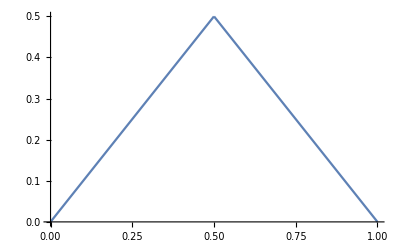

```mathematica
Plot[g0[x],{x,0,1}]
```

```mathematica
sol=DSolve[{
deq,
Y[0,t]==f0[t],
Y[1,t]==f1[t],
Y[x,0]==g0[x]},
Y[x,t],{x,t}]
```

{{Y[x,t]→(16 ⅇ^(-π^2 t 𝒟 K[1]^2) Cos[1/4 π K[1]] Sin[1/4 π K[1]]^3 Sin[π x K[1]])/(π^2 K[1]^2)K[1]1∞}}

```mathematica
Yf[x_,t_]:=Y[x,t]/.sol[[1]]
```

```mathematica
𝒟=1;
```

```mathematica
Yf[x_,t_]:=∑_(k=1)^100 (16 ⅇ^(-π^2 t 𝒟 k^2) Cos[1/4 π k] Sin[1/4 π k]^3 Sin[π x k])/(π^2 k^2)
```

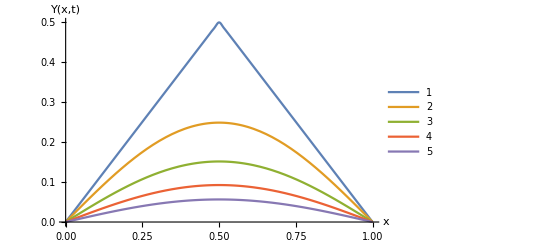

```mathematica
Plot[{Yf[x,0],Yf[x,0.05],Yf[x,0.1],Yf[x,0.15],Yf[x,0.2]},{x,0,1},AxesLabel->{"x","Y(x,t)"},PlotLegends->Automatic]
```